```mathematica
1+1
```

2

```mathematica
√49
```

7

```mathematica
(*Shift+Enter evaluates*)
```

```mathematica
f[x_]:=E^-x  (*Ctrl+6 did the exponent^333*)
```

```mathematica
E
```

ⅇ

```mathematica
N[E]
```

2.71828

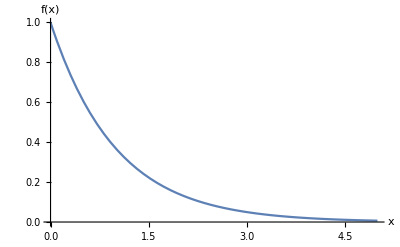

```mathematica
Plot[f[u],{u,0,5},AxesLabel->{"x","f(x)"}]
```

```mathematica
f[5] //N  (*// postfix evaluation*)
```

0.00673795

```mathematica
Integrate[f[u],{u,0,∞}]  (*ESC + inf + ESC gave me ∞*)
```

1

```mathematica
(a+b)^5//Expand
```

a^5+5 a^4 b+10 a^3 b^2+10 a^2 b^3+5 a b^4+b^5

```mathematica
(*SymPy in Python does a bit of that...*)
```

## Matrix operations

```mathematica
(*Went to the Format->Cell Menu and chose "section"*)
```

```mathematica
(*In mathematics {} "curly brakets" are used for SETS. However in mathematica they are used for lists... *)
```

```mathematica
A={
{0,-1,-2},(*First row*)
{1,0,-1} (*Second row*)
}
```

{{0,-1,-2},{1,0,-1}}

```mathematica
MatrixForm[A]
```

(0 | -1 | -2
1 | 0 | -1)

```mathematica
A//MatrixForm
```

(0 | -1 | -2
1 | 0 | -1)

```mathematica
? Table
```

```mathematica
AfromDef= Table[i-j,{i,1,2},{j,1,3}]
```

{{0,-1,-2},{1,0,-1}}

```mathematica
AfromDef //MatrixForm
```

(0 | -1 | -2
1 | 0 | -1)

```mathematica
A == AfromDef
```

True